# Lab 7

#### 1. How could we use the data from our pendulum simulation to compare with the analytical solution? Come up with a “figure-of-merit” – some single number – you can use to quantify how close the simulation and analytical answers are for a given angle. We can use the data from the pendulum simulation to compare the plot of the simulated pendulum and the plot given by the analytical solution ϕ[t] = ϕ0 Cos[ω0 t] . To come up with a “figure-of-merit”, we can integrate from t=0 to t=10 for the difference of the simulation and the analytical plots squared: ∫_0^10 (x[t]-y[t])^2ⅆt 2. In general, as the initial angle gets higher, what happens to the simulation results relative to the analytical results? In general, as the initial angle gets higher the simulation results start to lag behind the analytical results. This is because sin(ϕ) gets smaller the bigger the angle gets, and the difference eventually becomes too big to be able to use small angle approximation. 3. Make a plot of your “figure-of-merit” as a function of angle for at least 5 initial pendulum angles. Where does the small-angle approximation start to significantly deviate from the simulation (let’s say at the ≈10% level)? The small-angle approximation starts to significantly deviate from the simulation at around and angle of 40-50 degrees. 4. How would an increase in the mass of the pendulum bob change the dynamics (motion) of the system? An increase in the mass of the pendulum would not change the dynamics of the system. The mass is not in the final equation of motion for a pendulum and so would have no effect on the system.

```mathematica
ClearAll[penfunc,anFunc,iseMetric,angle,ϕ]
```

-Graphics-

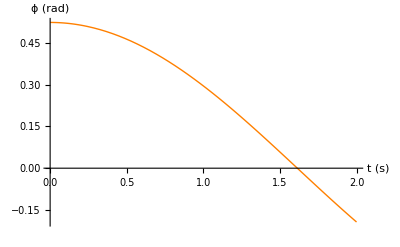

```mathematica
g=9.81;
L= 10;
ω0=Sqrt[g/L];

Plot[ϕ[t]==ϕ[0] Cos[ω0 t],{t,0,2}, AxesLabel->{"t (s)","y (rad)"}]

s=NDSolve[{ϕ''[t]==-(ω0^2)*Sin[ϕ[t]],ϕ[0]==30*Degree,ϕ'[0]==0},ϕ,{t,0,2}];

Plot[Evaluate[ϕ[t]/. s],{t,0,2},AxesLabel->{"t (s)","ϕ (rad)"},PlotStyle->{Orange,Thick}]
```

```mathematica
Clear[penfunc, ϕ,angle,penfunc, anFunc]
```

0.338631

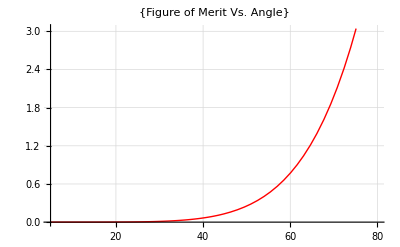

```mathematica
penfunc[ϕ0_]:=(NDSolve[{ϕ''[t]==-(ω0^2)*Sin[ϕ[t]],ϕ[0]==ϕ0*Degree,ϕ'[0]==0},ϕ,{t,0,10}])[[1]][[1]][[2]]
0.3386310487284805

anFunc[ϕ0_,t_]:=(ϕ0*Degree)*Cos[ω0*t]
iseMetric[ang_?NumericQ]:=NIntegrate[(penfunc[ang][t]-anFunc[ang,t])^2,{t,0,10}]

Plot[iseMetric[angle],{angle,5,80},GridLines->Automatic,PlotStyle->{Red,Thick},PlotLabel->{"Figure of Merit Vs. Angle"}]
```